```mathematica
Clear["Global`*"];
pp = 3;
clist=Table[Subscript[c, α,n],{n,0,pp}]/. {{α->x},{α->y},{α->z}}//Flatten;

Rot[ϕ_]={{Cos[ϕ], Sin[ϕ],0}, {-Sin[ϕ], Cos[ϕ], 0}, {0,0,1}};

style = Sequence[PlotStyle->Directive[Thickness[0.001],White]];
U[t_,t0_,t1_,u0_,u1_]=u0* Sech[(t-t0)*2]^10+u1*Sech[(t-t1)*2];

Get3DView[gfx_]:=Options[Unevaluated[gfx],{ViewCenter,ViewVector,ViewVertical,ViewPoint}];

Manipulate[
global = {u1,u2,m2,xf,v,o,ct,n,t1,t2,cTanh,at0,at4,hueG,zIrreg,nRot};

F[t_]={xf, (v t+ct)Cos[o t^n],z0+(v t+ct)Sin[o t^n]};
Gmod[t_]=(1-Cos[t*m1]/m2)*Tanh[(t-u1)*2];
G[t_]={Gmod[t]* Sin[t],Gmod[t]* Cos[t], t/4*Tanh[(t-u1)*cTanh]+Sin[t*m1]*zIrreg};

S[t_]=Sum[Subscript[c, α,n] t^n,{n,0,pp}]/. {{α->x},{α->y},{α->z}};
(*cc1=Solve[{S[t1]==F[t1],S[u1]==G[u1],S'[t1]==-F'[t1],S'[u1]==G'[u1](*,S''[t1]==-F''[t1],S''[u1]==G''[u1]*)},clist] //First;
cc2=Solve[{S[t2]==F[t2],S[u2]==G[u2],S'[t2]==F'[t2],S'[u2]==-G'[u2](*,S''[t2]==-F''[t2],S''[u2]==G''[u2]*)},clist] //First;*)
(*cc=Solve[{S[u1]==G[u1],S[u2]==G[u2],S'[u1]==-G'[u1],S'[u2]==-G'[u2],S''[u1]=={G''[u1][[1]]*sdx2,G''[u1][[2]]*sdx2,sdz2},S''[u2]=={G''[u2][[1]]*sdx2,G''[u2][[2]]*sdx2,-sdz2}},clist] //First;*)

(*cc=Solve[{S[at0]==G[u1],S'[at0]==-G'[u1],S[at4]==G[u2], S'[at4]==-G'[u2],S[at1]=={ax1,ay1,az1},S[at2]=={ax2,ay2,az2},S[at3]=={ax3,ay3,az3}},clist] //First;*)
cc=Solve[{S[at0]==G[u1],S'[at0]==-G'[u1],S[at4]==G[u2], S'[at4]==-G'[u2]},clist] //First; (* {-G'[u2][[1]],-G'[u2][[2]],0} *)

(*tRebend = t /. NSolve[D[((S[t][[1]])^2+(S[t][[2]])^2)^(1/2)/.cc, t]==0, t][[2]];
zRebend=S[tRebend][[3]]/.cc;*)

Δϕ=2π/nRot;

(*ColorData[colors][1-t*hueG]*)
(*Hue[t*hueG]*)
(*Hue[U[t,at0,at4,u1*hueG,u2*hueG],U[t,at0,at4,1,1],1]*)

show = Show[
(*ParametricPlot3D[Table[Rot[ϕ]. F[t], {ϕ, 0, 2π,Δϕ}]//Evaluate, {t, t1, t2}, PlotPoints->1000,  Evaluate[style], ColorFunction->Function[{x,y,z},RGBColor[0,0,1]],Background->Black] ,*)
ParametricPlot3D[Table[Rot[ϕ]. (S[t]/.cc),{ϕ, 0, 2π,Δϕ}]//Evaluate,{t, at0, at4},Evaluate[style], Background->Black, (*ViewPoint->Right,*) ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}, {0.25, White}, {0.8, White}, {1,topColor}}, Rescale[t, {at0,at4}]]],ColorFunctionScaling->False],
(*Graphics3D[{PointSize[0.01],Green,  Point[{ax1,ay1,az1}],Yellow, Point[{ax2,ay2,az2}],Red,  Point[{ax3,ay3,az3}]}],*)
(*ParametricPlot3D[Table[Rot[ϕ]. (S[t]/.cc1),{ϕ, 0, 2π,Δϕ}]//Evaluate,{t, u1, t1},Evaluate[style],ColorFunction->Function[{x,y,z},RGBColor[1,E^(sc*z)-1,E^(sc*z)-1]]],
ParametricPlot3D[Table[Rot[ϕ]. (S[t]/.cc2),{ϕ, 0, 2π,Δϕ}]//Evaluate,{t, t2, u2},Evaluate[style]],*)
ParametricPlot3D[Table[Rot[ϕ]. G[t], {ϕ, 0, 2π,Δϕ}] //Evaluate,{t,u1,u2},Evaluate[style],ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}}~Join~Table[{midColorsPos[[i]], midColors[[i]]}, {i,1,middleColorsCnt}]~Join ~{{1,topColor}}, Rescale[t, {u1,u2}]]], ColorFunctionScaling->False],  
(*Graphics3D[{Opacity[0.4],InfinitePlane[{0,0,zRebend},{{1,0,0},{1,1,0}}]}],*)
ImageSize->Scaled[0.6], Boxed->False,PlotRangePadding->0.1, Axes->False,ViewPoint->{0,0,-camH}],

(*ResourceFunction["ExportRotatingGIF"]["C:\\Users\\pasha\\Downloads\\3d.gif", show, "Graphics3DOptions"->{Background->Black}],  *)

{{u1, 0.21}, -π, 2π, ControlType->None},
{{u2, 25}, 6π, 10π, ControlType->None},
{{m2,4.5},1,50},
{{xf,0.24}, 0, 10},
{{v,0.1}, 0.01, 1},
{{o, 1.5},1,10},
{{ct, 0.2},0,1},
{{n,1.03},0.3,10},
{t1,π/10,π, ControlType->None},
{{t2, 2.11},0,3π, ControlType->None},
{{cTanh, 1}, 0.01, 2},
{{at0, 4.8}, -π, 2π, ControlType->None},
{{at4, 8.8}, 3, 8π, ControlType->None},
{{hueG, 0.032}, 0.024, 0.04},
{{zIrreg, 0.15}, 0, 0.6},
{{nRot, 8}, 1,14,1,ControlType->PopupMenu},
{{camH, 1}, 0.5, 10},
{{m1,8.9},4,20, 0.1},
(*{{colors,"Rainbow"},ColorData["Gradients"],ControlType->PopupMenu},*)
{topColor, Hue[0.8]},
{bottomColor, Hue[0]},

{{middleColorsCnt, 0}, 0, 5, 1, ControlType->Setter},
{{midColors,RandomColor[10]},ControlType->None},
{{midColorsPos,RandomReal[1, 10]//Sort},ControlType->None},
Dynamic[Column[Outer[
Row[{ColorSetter[Dynamic[midColors[[#1]]]], Slider[Dynamic[midColorsPos[[#1]]], Appearance->"Labeled"]}, "   "]&,
Range[middleColorsCnt]
]]],

Button["1",m1=1.19; zIrreg=0.278],
Button["2",m1=2; zIrreg=0.15],
Button["Reset",Replace[Typeset`specs,{{{Hold[var_Symbol],val_},___}:>(var=val),{Hold[var_Symbol],val_,___}:>(var=val)},1]],SaveDefinitions->True

]

(*//DiscretizeGraphics
PlotTheme->"Marketing"
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->Function[{x,y,z},Hue[z]]]
coords=pic["Coordinates"]; 
ListPointPlot3D[MapThread[Tooltip,{coords,coords}]];
Show[%,pic]*)
```

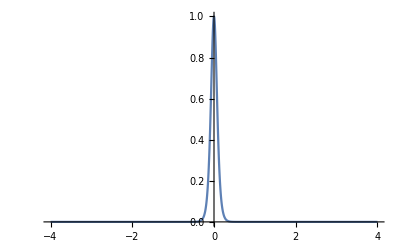

```mathematica
Plot[Tanh'[x*10],{x,-4,4}, PlotRange->All]
```

```mathematica
Hue["white"]
```

Hue[0., 0., 1.]

```mathematica
ColorConvert[{255,255,255}, "HSB"]//InputForm
```

Hue[0., 0., 1.]

```mathematica
Hue[0., 0., 1.]
```

Hue[0., 0., 1.]

```mathematica
Tanh'[x]
```

Sech[x]^2

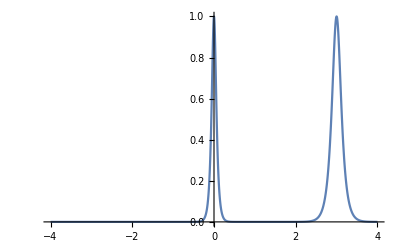

```mathematica
Plot[Sech[x*20]+Sech[(x-3)*10],{x,-4,4}, PlotRange->All]
```

```mathematica
U[t_,t0_,t1_,u0_,u1_]=u0* Sech[(t-t0)*50]+u1*Sech[(t-t1)*50];
Manipulate[
Plot[U[t,t0,t1,u0,u1],{t,t0,t1},PlotRange->All],
{t0, 1, 2},{t1, 4, 5},
{u0, 1, 10},{u1, 1, 10}

]
```

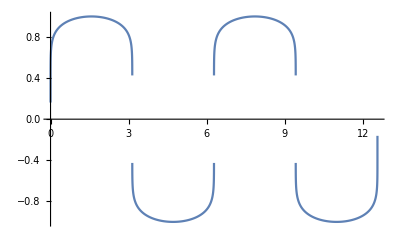

```mathematica
Plot[{Sign[Sin[t]]* (Abs[Sin[t]])^(1/10)}, {t, 0, 4π}, PlotRange->All, PlotPoints->1000]
```

```mathematica
S[t]/.cc//CForm
(*ExportString[S[t]/.cc, "JSON"]*)
```

List(16.899564792188887 - 8.196532473537694*t + 1.282913717449209*Power(t,2) - 0.06433142514140014*Power(t,3),
   35.84995852946314 - 15.49672745166052*t + 2.108773886337624*Power(t,2) - 0.09089099666080262*Power(t,3),
   42.12520166664752 - 20.854024263630826*t + 3.2559245428517545*Power(t,2) - 0.15376601027658085*Power(t,3))

```mathematica
(*Solve[D[((S[t][[1]])^2+(S[t][[2]])^2)^(1/2)/.cc, t]==0, t]*)
```

```mathematica
(*D[((S[t][[1]])^2+(S[t][[2]])^2)^(1/2)/.cc, t]//Simplify*)
```

```mathematica
cc
```

{c_(x,0)→19.8166,c_(x,1)→-9.81119,c_(x,2)→1.57586,c_(x,3)→-0.0816589,c_(y,0)→41.9347,c_(y,1)→-18.6957,c_(y,2)→2.64941,c_(y,3)→-0.119697,c_(z,0)→55.3784,c_(z,1)→-27.8595,c_(z,2)→4.44917,c_(z,3)→-0.218143}

```mathematica
global
```

{0.21,25,4.5,0.24,0.1,1.5,0.2,1.03,π/10,2.11,1,4.8,8.8,0.032,0.15,12}

```mathematica
data = {};
{u1,u2,m2,xf,v,o,ct,n,t1,t2,cTanh,at0,at4,hueG,zIrreg,nRot}=global;
nRot=12;
Δϕ=2π/nRot;
topColor = Hue[0.8];
bottomColor = Hue[0];
```

```mathematica
m1Array = {12.3,15,6.9,4.4,7.,7.4,9.,8.9,8.4,4.1,6.6,7.5,8.5,7.6,8.6,16.92}; (*top 8*)
m1Array = {7.7, 16.6, 15.6,  16.92}; (*top 8 excluded*)
m1Array = {8.6}; 
(*m1Array = {6.9,4.4,7.4,9.,8.9,8.4,4.1,6.6,7.5,8.5,7.6,8.6}; *)(*top 8 min*)
(*m1Array = {4.1,4.4,5.6,6.6,6.7,6.9,7,7.1,7.2,7.4,7.5,7.6,7.7,8.2,8.4,8.5,8.6,8.7,8.9,9.8,12,12.3};*) (*bot 8*)
(*m1Array = {5.1,5.4,5.6,5.7,6.4,6.5,6.6,6.7,6.9,7,7.1,9,9.8,10.9,11,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,12.2,12.5,12.6,12.7,12.8,12.9,13,13.1,13.2,14.9,15,16.7,17.2,17.4,17.5,18.5,18.6,19.2};*) (*bot 6*)
(*19.1, 7.7, 16.6, 9.1, 15.6, 16.8,*)

Do[
F[t_]={xf, (v t+ct)Cos[o t^n],z0+(v t+ct)Sin[o t^n]};
Gmod[t_]=(1-Cos[t*m1]/m2)*Tanh[(t-u1)*2];
G[t_]={Gmod[t]* Sin[t],Gmod[t]* Cos[t], t/4*Tanh[(t-u1)*cTanh]+Sin[t*m1]*zIrreg};
S[t_]=Sum[Subscript[c, α,n] t^n,{n,0,pp}]/. {{α->x},{α->y},{α->z}};
cc=Solve[{S[at0]==G[u1],S'[at0]==-G'[u1],S[at4]==G[u2], S'[at4]==-G'[u2]} ,clist] //First;
AppendTo[data, {"m1"-> m1, "cc" -> clist/.cc}];

show = Show[
ParametricPlot3D[Table[Rot[ϕ]. (S[t]/.cc),{ϕ, 0, 2π,Δϕ}]//Evaluate,{t, at0, at4},Evaluate[style], Background->Black, ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}, {0.25, White}, {0.8, White}, {1,topColor}}, Rescale[t, {at0,at4}]]],ColorFunctionScaling->False],
ParametricPlot3D[Table[Rot[ϕ]. G[t], {ϕ, 0, 2π,Δϕ}] //Evaluate,{t,u1,u2},Evaluate[style],ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}}~Join~{{1,topColor}}, Rescale[t, {u1,u2}]]], ColorFunctionScaling->False],  
ImageSize->Scaled[0.4], Boxed->False,Axes->False,
ViewPoint->{0,0,1}];

Export[StringForm["d:\\Work\\GA\\tmp\\GA1\\img\\h=1\\mint svg\\m1_``.png", m1]// ToString,show];
,

{m1, m1Array}
];
```

```mathematica
For[  
m1=4,
m1 <=20,
m1+=0.1,


F[t_]={xf, (v t+ct)Cos[o t^n],z0+(v t+ct)Sin[o t^n]};
Gmod[t_]=(1-Cos[t*m1]/m2)*Tanh[(t-u1)*2];
G[t_]={Gmod[t]* Sin[t],Gmod[t]* Cos[t], t/4*Tanh[(t-u1)*cTanh]+Sin[t*m1]*zIrreg};
S[t_]=Sum[Subscript[c, α,n] t^n,{n,0,pp}]/. {{α->x},{α->y},{α->z}};
cc=Solve[{S[at0]==G[u1],S'[at0]==-G'[u1],S[at4]==G[u2], S'[at4]==-G'[u2]} ,clist] //First; 

(*tRebend = t /. NSolve[D[((S[t][[1]])^2+(S[t][[2]])^2)^(1/2)/.cc, t]==0, t][[2]];
zRebend=S[tRebend][[3]]/.cc;*)
AppendTo[data, {"m1"-> m1, (*"z"-> zRebend,*) "cc" -> clist/.cc}];

show = Show[
ParametricPlot3D[Table[Rot[ϕ]. (S[t]/.cc),{ϕ, 0, 2π,Δϕ}]//Evaluate,{t, at0, at4},Evaluate[style], Background->Black, ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}, {0.25, White}, {0.8, White}, {1,topColor}}, Rescale[t, {at0,at4}]]],ColorFunctionScaling->False],
ParametricPlot3D[Table[Rot[ϕ]. G[t], {ϕ, 0, 2π,Δϕ}] //Evaluate,{t,u1,u2},Evaluate[style],ColorFunction->Function[{x,y,z,t},Blend[{{0,bottomColor}}~Join~{{1,topColor}}, Rescale[t, {u1,u2}]]], ColorFunctionScaling->False],  
ImageSize->Scaled[0.6], Boxed->False,Axes->False,
ViewPoint->{0,0,-1}];

Export[StringForm["dd:\\Work\\GA\\tmp\\GA1\\img\\h=1\\rot=8 svg\\m1_``.svg", m1]// ToString,show, ImageResolution->60];
];
```

```mathematica
data
```

{{m1→4.1,cc→{19.3998,-9.52689,1.51781,-0.0781334,59.6042,-27.752,4.15086,-0.199205,59.5807,-29.5115,4.64781,-0.225127}},{m1→4.4,cc→{22.5527,-11.1918,1.80194,-0.093575,50.2824,-22.7397,3.28061,-0.151162,53.0099,-26.0552,4.06341,-0.19392}},{m1→5.6,cc→{18.8504,-9.1802,1.45004,-0.0740953,66.6784,-31.2549,4.71348,-0.228347,58.593,-29.1482,4.61207,-0.224294}},{m1→6.6,cc→{18.5373,-8.9726,1.40818,-0.0715544,71.4923,-33.6204,5.09047,-0.247748,56.5463,-28.3697,4.52594,-0.221553}},{m1→6.7,cc→{24.3556,-12.0561,1.9358,-0.100251,38.624,-16.1532,2.09409,-0.0844213,47.8853,-23.8613,3.77149,-0.181733}},{m1→6.9,cc→{22.6836,-11.163,1.78216,-0.0918904,61.0638,-27.9984,4.1115,-0.193507,42.6542,-21.1432,3.31226,-0.156724}},{m1→7,cc→{21.5571,-10.5539,1.67544,-0.0859085,36.9106,-15.2261,1.93653,-0.0763446,61.4598,-31.1866,5.04422,-0.251679}},{m1→7.1,cc→{18.3995,-8.878,1.38872,-0.0703589,73.8408,-34.7687,5.27256,-0.257079,55.1129,-27.8222,4.46451,-0.219538}},{m1→7.2,cc→{24.7742,-12.2571,1.96705,-0.101824,39.382,-16.4535,2.12995,-0.0857135,44.3226,-22.1913,3.51887,-0.169354}},{m1→7.4,cc→{22.6288,-11.1125,1.77028,-0.0911105,63.7741,-29.3363,4.32554,-0.204537,39.6149,-19.7652,3.11165,-0.147248}},{m1→7.5,cc→{22.1776,-10.8618,1.72498,-0.0884744,36.1707,-14.7315,1.83629,-0.0702368,58.6385,-29.9339,4.86674,-0.243555}},{m1→7.6,cc→{18.2753,-8.7904,1.37042,-0.069226,76.1108,-35.8746,5.44726,-0.266004,53.4259,-27.1774,4.3919,-0.217139}},{m1→7.7,cc→{25.1632,-12.4423,1.99557,-0.103247,40.3228,-16.8502,2.18223,-0.0878964,40.3294,-20.3296,3.23879,-0.155699}},{m1→8.2,cc→{25.5181,-12.6094,2.02102,-0.104503,41.4447,-17.3435,2.25116,-0.0909889,35.9462,-18.2949,2.93404,-0.140901}},{m1→8.4,cc→{22.4312,-10.9649,1.73854,-0.0891171,69.5765,-32.2156,4.78864,-0.228513,32.8027,-16.7239,2.67682,-0.127085}},{m1→8.5,cc→{23.4404,-11.4895,1.82614,-0.0937212,34.6413,-13.717,1.63159,-0.0577948,51.5623,-26.7701,4.41393,-0.222585}},{m1→8.6,cc→{18.0701,-8.6386,1.3379,-0.0671837,80.2992,-37.9017,5.76535,-0.282162,49.3917,-25.6382,4.21866,-0.211413}},{m1→8.7,cc→{25.8346,-12.7565,2.04309,-0.105578,42.745,-17.9331,2.33682,-0.0950032,31.222,-16.1096,2.6079,-0.125117}},{m1→8.9,cc→{22.2876,-10.8678,1.71876,-0.087911,72.6192,-33.733,5.03392,-0.241267,29.1217,-15.1025,2.44872,-0.116688}},{m1→9.8,cc→{19.8264,-9.51819,1.48025,-0.074544,56.2628,-24.9591,3.52365,-0.159542,54.6596,-29.3144,4.98203,-0.258643}},{m1→12,cc→{27.495,-13.5195,2.15561,-0.110916,29.5971,-10.4517,0.982211,-0.0186194,16.73,-10.9455,2.09971,-0.11286}},{m1→12.3,cc→{22.3427,-10.7755,1.68382,-0.0851365,48.8424,-20.6583,2.73225,-0.114236,37.4185,-22.1268,4.04265,-0.219481}}}

```mathematica
Export["d:\\Work\\GA\\Interactive\\Spirals\\src\\spiral_bot_6.json", data, "JSON"]
```

d:\Work\GA\Interactive\Spirals\src\spiral_bot_6.json

```mathematica
StringForm["The value of Pi is ``",NumberForm[N[Pi],3]] // ToString
```

The value of Pi is 3.14

```mathematica
Manipulate[ParametricPlot3D[{10*Sin[t], 10*Cos[t], t*4},{t,0,2 π},

ColorFunction->Function[{x,y,t},ColorData[color]@t],

Axes->None, Background->Black],

{{color,"TemperatureMap"},ColorData["Gradients"],ControlType->PopupMenu}]
```

```mathematica
Manipulate[
{Take[midColors, n],Take[midColorsPos, n],Blend[ {{0,Red}}~Join~ Table[{midColorsPos[[i]], midColors[[i]]}, {i,1,n}]~Join~{{1,Blue}}, 0.5]},
{{n,1},0,10,1},
{{midColors,RandomColor[10]},ControlType->None},
{{midColorsPos,RandomReal[1, 10]//Sort},ControlType->None},
Dynamic[Column[Outer[
Row[{ColorSetter[Dynamic[midColors[[#1]]]], Slider[Dynamic[midColorsPos[[#1]]], Appearance->"Labeled", Background->Dynamic[midColors[[#1]]]]}, "   "]&,
Range[n]
]]]
]
```

```mathematica
Blend[{{0,Red}}~Join~{{0.0953800308988,RGBColor[0.3374262794042473, 0.8220070787798688, 0.4897774391670011]}, {0.2,RGBColor[0.3374262794042473, 0.8220070787798688, 0.4897774391670011]}}, 0]
```

RGBColor[1, 0, 0]